This notebook will be used to store all the exercises related to Mathematica of the C2 project for the course Writing and Presenting Maths.

Exercise 1.2:

Write a program to compute the first 20 digits in the decimal expansion of $1/\sqrt{2}$.

```mathematica
x= 1/Sqrt[2];
digits={0};
For[i=0,i<20, i++,
  x= 10x;
  a=Floor[x];
  x= x-a;
  digits=Append[digits,a];
];
Print[digits];
```

{0,7,0,7,1,0,6,7,8,1,1,8,6,5,4,7,5,2,4,4,0}

Exercise 3.1.2

The work is entirely theoretical, but I’ll write a program to spot the dynamics of the system. We spotted (and proved) that in base 3, multiplying by 1/3=0.1 is exactly shifting the decmial to the right and filling with a 0. Moreover, we also proved that adding 2/3=0.2 is exactly adding only the first digit of the decimal expansion. I will use these rules to write the program

```mathematica
w1={{"0.","0.1"}, {"0.2","1."}};
mult01[tup_]:=
  Module[{t0},
    t0=
    {StringInsert[tup[[1]], "0", 3],StringInsert[tup[[2]], "0", 3]}];

wn[wn1_]:= 
  Module[{m01},
    m01= mult01[wn1];
    {m01, add02[m01]}];
mult01[w1[[1]]]
mult01[w1[[2]]]
```

```mathematica
w1in3={{0, 1/3},{2/3, 1}};
mult01in3[tup_]:={tup[[1]]*1/3,tup[[2]]*1/3};
add02in3[tup_]:={tup[[1]]+2/3,tup[[2]]+2/3};


wnin3[wn1_]:= 
  Module[{m01,m02},
    m01= {};
    For[i=1,i<=Length[wn1],i++,
      m01=Append[m01, mult01in3[wn1[[i]]]];
    ];
    m02={};
    For[i=1,i<=Length[wn1],i++,
      m02=Append[m02, add02in3[m01[[i]]]];
    ];
    Union[m01, m02]];

wnin3[w1in3]
wnin3[wnin3[w1in3]]
```

{{0,1/9},{2/9,1/3},{2/3,7/9},{8/9,1}}

{{0,1/27},{2/27,1/9},{2/9,7/27},{8/27,1/3},{2/3,19/27},{20/27,7/9},{8/9,25/27},{26/27,1}}

```mathematica
BaseForm[(3^^0.1)*(3^^0.1),3]
BaseForm[(3^^0.1)+(3^^0.1),3]
```

0.01_3

0.2_3

Exercise 3.2.1

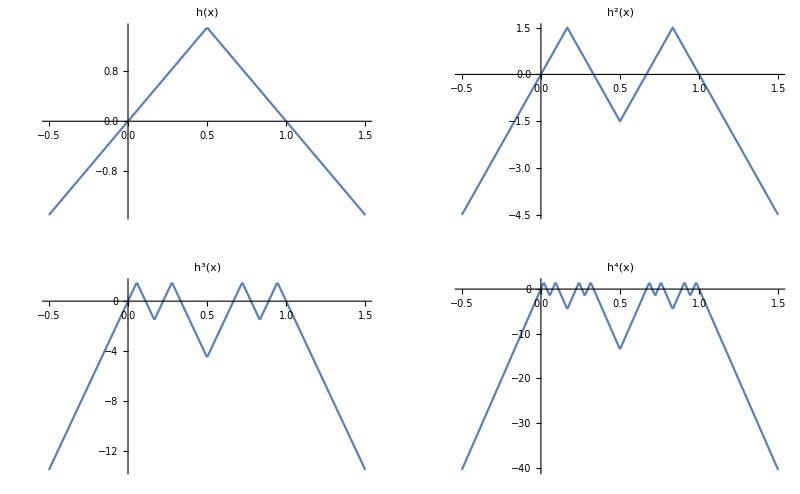

```mathematica
Clear[h];
hh[xx_]:=Piecewise[{{3xx, xx<=1/2},{3-3xx, xx>=1/2}}]
kh[xx_,kk_]:=Module[{},
  Apply[Composition,Table[hh,kk]][xx]
]
h1=Plot[kh[x,1], {x,-.5,1.5}, PlotLabel->ToExpression["h(x)", TeXForm]];
h2=Plot[ kh[ x,2], {x, -.5, 1.5}, PlotLabel->ToExpression["h^2(x)", TeXForm]];
h3=Plot[ kh[ x,3], {x, -.5, 1.5}, PlotLabel->ToExpression["h^3(x)", TeXForm]];
h4=Plot[ kh[x,4], {x, -.5, 1.5}, PlotLabel->ToExpression["h^4(x)", TeXForm]];
gg =GraphicsGrid[{{h1,h2},{h3,h4}}, Background->None]
(*Export[gg, "test3.png"]*)
```

20

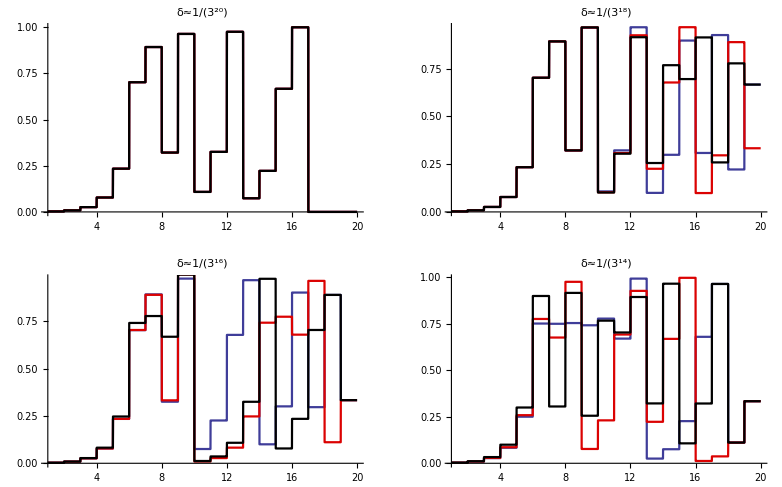

```mathematica
ftt[x_]:=1/3^x
nn=20
sequences=Tuples[{0,2},nn];
ft[i_]:=Sum[sequences[[i]][[n]]*ftt[n],{n,1,nn} ]
(*points = Array[ft, 2^nn];*)

(*
For[i=1,i<=2, i++,
  plots=Append[plots, Plot[kh[ft[i],n],{n,1,20}, PlotStyle->i]]
]
For[i=101,i<=102, i++,
  plots=Append[plots, Plot[kh[ft[i],n],{n,1,20}, PlotStyle->i]]
]
For[i=10001,i<=10002, i++,
  plots=Append[plots, Plot[kh[ft[i],n],{n,1,20}, PlotStyle->i-10000+1]]
]*)
plots={};
plots=Append[plots, Plot[kh[ft[10001],n],{n,1,20}, PlotStyle->1]];
plots=Append[plots, Plot[kh[ft[10001],n],{n,1,20}, PlotStyle->2]];
plots=Append[plots, Plot[kh[ft[10001],n],{n,1,20}, PlotStyle->3]];
p1=Show[plots, PlotLabel->ToExpression["\delta\approx 3^{-20}", TeXForm,HoldForm]];
plots={};
plots=Append[plots, Plot[kh[ft[10010],n],{n,1,20}, PlotStyle->1]];
plots=Append[plots, Plot[kh[ft[10020],n],{n,1,20}, PlotStyle->2]];
plots=Append[plots, Plot[kh[ft[10030],n],{n,1,20}, PlotStyle->3]];
p2=Show[plots, PlotLabel->ToExpression["\delta\approx 3^{-18}", TeXForm,HoldForm]];
plots={};
plots=Append[plots, Plot[kh[ft[10100],n],{n,1,20}, PlotStyle->1]];
plots=Append[plots, Plot[kh[ft[10200],n],{n,1,20}, PlotStyle->2]];
plots=Append[plots, Plot[kh[ft[10300],n],{n,1,20}, PlotStyle->3]];
p3=Show[plots, PlotLabel->ToExpression["\delta\approx 3^{-16}", TeXForm,HoldForm]];
plots={};
plots=Append[plots, Plot[kh[ft[11000],n],{n,1,20}, PlotStyle->1]];
plots=Append[plots, Plot[kh[ft[12000],n],{n,1,20}, PlotStyle->2]];
plots=Append[plots, Plot[kh[ft[13000],n],{n,1,20}, PlotStyle->3]];
p4=Show[plots, PlotLabel->ToExpression["\delta\approx 3^{-14}", TeXForm,HoldForm]];
GraphicsGrid[{{p1,p2},{p3,p4}},Background->White]
```